```mathematica
PiecewiseExpand[BernsteinBasis[n,k,x],0<x<1&&n>=k>0]
```

(1-x)^(-k+n) x^k Binomial[n,k]

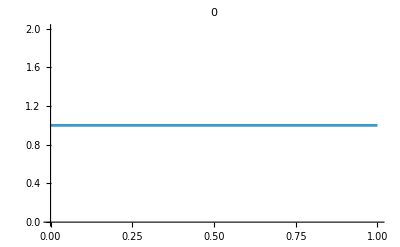
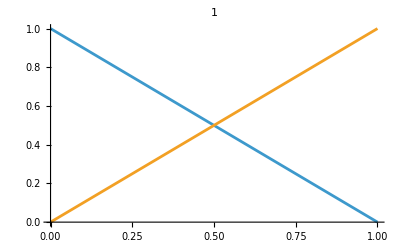
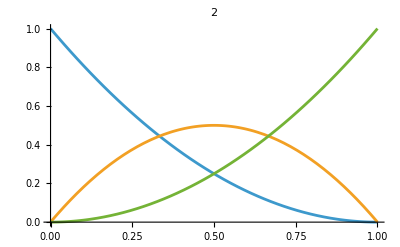
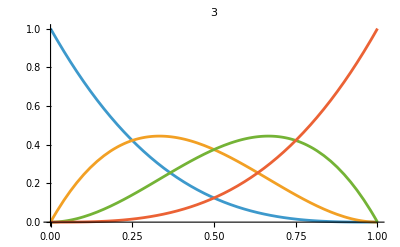

```mathematica
Table[Plot[Evaluate[Table[BernsteinBasis[n,k,x],{k,0,n}]],{x,0,1},PlotLabel->n],{n,0,3}]
```

```mathematica
And@@Flatten@Table[Binomial[n,m]==lim_(ϵ(->)_Complexes 0) Gamma[n+ϵ+1]/(Gamma[m+ϵ+1] Gamma[-m+n+ϵ+1]),{n,-5,5},{m,-5,5}]
```

True

```mathematica
And@@Flatten@Table[Binomial[n,m]==Piecewise[{{((-1)^m Pochhammer[-n,m])/(m!), m≥0}, {((-1)^(-m+n) Pochhammer[-n,-m+n])/((-m+n)!), m≤n}}],{n,-5,5},{m,-5,5}]
```

True

```mathematica
Assuming[{n,m}∈Integers,FullSimplify@FunctionExpand[Binomial[n,m]]]
```

Piecewise[{{Pochhammer[1-m+n,m]/(m!), m≥0}, {Pochhammer[1+m,-m+n]/((-m+n)!), n≥m}, {0, True}}]